## Generators for base 6

```mathematica
Length [Keys[allGraphs6]]
```

53071

```mathematica
OnlyOneMinimum[k_]:=Block[{formula = allGraphs6[k,"colofour"], sizes,min},
sizes=Map[Length[SymbolToSets[#]]&,ListofVars[formula]];
min=Min[sizes];
Length[Select[sizes,#==min&]]==1
]
```

```mathematica
allGraphs6GeneratorAtomKeysPart1=Select[Sort[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]],OnlyOneMinimum[#]&];
```

```mathematica
Length[allGraphs6GeneratorAtomKeysPart1]
```

6203

```mathematica
allGraphs6[7174344,"graph"]
```

-Graphics-

```mathematica
Monitor[Table[BaseGenerators[allGraphs6[k,"colofour"]],{k,RandomSample[Sort[Keys[allGraphs6]],10000]}];,k]
```

```mathematica
allGraphs6GeneratorAtomKeysPart2=Select[allGraphs6GeneratorAtomKeysPart1,VertexCount[allGraphs6[#,"graph"]]==6&&Length[Flatten[Values[BaseGenerators[allGraphs6[#,"colofour"]]]]]==1&];Length[allGraphs6GeneratorAtomKeysPart2]
```

203

```mathematica
allGraphs6GeneratorAtomKeys=Sort[allGraphs6GeneratorAtomKeysPart2,CompareSymbols[First[Flatten[Values[BaseGenerators[allGraphs6[#1,"colofour"]]]]],First[Flatten[Values[BaseGenerators[allGraphs6[#2,"colofour"]]]]]]&];Length[allGraphs6GeneratorAtomKeys]
```

203

## First define the generator base

```mathematica
Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs6[k,"graph"]]]},
allGraphs6[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs6GeneratorAtomKeys}
]
```

{g1x2x3x4x5x6,g1x2x3x4x56,g1x2x3x45x6,g1x2x3x46x5,g1x2x34x5x6,g1x2x35x4x6,g1x2x36x4x5,g1x23x4x5x6,g1x24x3x5x6,g1x25x3x4x6,g1x26x3x4x5,g12x3x4x5x6,g13x2x4x5x6,g14x2x3x5x6,g15x2x3x4x6,g16x2x3x4x5,g1x2x34x56,g1x2x35x46,g1x2x36x45,g1x23x4x56,g1x23x45x6,g1x23x46x5,g1x24x3x56,g1x24x35x6,g1x24x36x5,g1x25x3x46,g1x25x34x6,g1x25x36x4,g1x26x3x45,g1x26x34x5,g1x26x35x4,g12x3x4x56,g12x3x45x6,g12x3x46x5,g12x34x5x6,g12x35x4x6,g12x36x4x5,g13x2x4x56,g13x2x45x6,g13x2x46x5,g13x24x5x6,g13x25x4x6,g13x26x4x5,g14x2x3x56,g14x2x35x6,g14x2x36x5,g14x23x5x6,g14x25x3x6,g14x26x3x5,g15x2x3x46,g15x2x34x6,g15x2x36x4,g15x23x4x6,g15x24x3x6,g15x26x3x4,g16x2x3x45,g16x2x34x5,g16x2x35x4,g16x23x4x5,g16x24x3x5,g16x25x3x4,g1x2x3x456,g1x2x345x6,g1x2x346x5,g1x2x356x4,g1x234x5x6,g1x235x4x6,g1x236x4x5,g1x245x3x6,g1x246x3x5,g1x256x3x4,g123x4x5x6,g124x3x5x6,g125x3x4x6,g126x3x4x5,g134x2x5x6,g135x2x4x6,g136x2x4x5,g145x2x3x6,g146x2x3x5,g156x2x3x4,g12x34x56,g12x35x46,g12x36x45,g13x24x56,g13x25x46,g13x26x45,g14x23x56,g14x25x36,g14x26x35,g15x23x46,g15x24x36,g15x26x34,g16x23x45,g16x24x35,g16x25x34,g1x23x456,g1x234x56,g1x235x46,g1x236x45,g1x24x356,g1x245x36,g1x246x35,g1x25x346,g1x256x34,g1x26x345,g12x3x456,g12x345x6,g12x346x5,g12x356x4,g123x4x56,g123x45x6,g123x46x5,g124x3x56,g124x35x6,g124x36x5,g125x3x46,g125x34x6,g125x36x4,g126x3x45,g126x34x5,g126x35x4,g13x2x456,g13x245x6,g13x246x5,g13x256x4,g134x2x56,g134x25x6,g134x26x5,g135x2x46,g135x24x6,g135x26x4,g136x2x45,g136x24x5,g136x25x4,g14x2x356,g14x235x6,g14x236x5,g14x256x3,g145x2x36,g145x23x6,g145x26x3,g146x2x35,g146x23x5,g146x25x3,g15x2x346,g15x234x6,g15x236x4,g15x246x3,g156x2x34,g156x23x4,g156x24x3,g16x2x345,g16x234x5,g16x235x4,g16x245x3,g1x2x3456,g1x2345x6,g1x2346x5,g1x2356x4,g1x2456x3,g1234x5x6,g1235x4x6,g1236x4x5,g1245x3x6,g1246x3x5,g1256x3x4,g1345x2x6,g1346x2x5,g1356x2x4,g1456x2x3,g123x456,g124x356,g125x346,g126x345,g134x256,g135x246,g136x245,g145x236,g146x235,g156x234,g12x3456,g1234x56,g1235x46,g1236x45,g1245x36,g1246x35,g1256x34,g13x2456,g1345x26,g1346x25,g1356x24,g14x2356,g1456x23,g15x2346,g16x2345,g1x23456,g12345x6,g12346x5,g12356x4,g12456x3,g13456x2,g123456}

```mathematica
repFullToGen6=ToRules[
Reduce[
Table[
allGraphs6[k,"colofourgenerator"]==allGraphs6[k,"colofour"]
,
{k,allGraphs6GeneratorAtomKeys}
],
Table[allGraphs6[k,"colofour"],{k,allGraphs6AtomKeys}]
]
];
```

```mathematica
Length[repFullToGen6]
```

203

```mathematica
Monitor[
Table[
allGraphs6[k,"colofourgenerator"]=Simplify[allGraphs6[k,"colofour"]/.repFullToGen6],
{k,Sort[Keys[allGraphs6]]}
],k];
```

```mathematica
Put[allGraphs6,"d:\\Saved\\Complete6bbb.m"]
```

## Now define the base basic data

```mathematica
Bases6=Association[];
```

```mathematica
Bases6["C"]=Association[];
```

```mathematica
Bases6["C","Colofour"]="colofour";
```

```mathematica
Bases6["E"]=Association[];
```

```mathematica
Bases6["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases6["G"]=Association[];
```

```mathematica
Bases6["G","Colofour"]="colofourgenerator";
```

```mathematica
allBases6=Keys[Bases6]
```

{C,E,G}

## Compute keys and variables

```mathematica
.
```

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Monitor[Table[Bases6[base,"AtomKeys"]=Sort[Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,Bases6[base,"Colofour"]]]]==1&],MyComp[allGraphs6[#1,Bases6[base,"Colofour"]],allGraphs6[#2,Bases6[base,"Colofour"]]]&]
,{base,allBases6}],base];
```

```mathematica
Table[Bases6[base,"Variables"]=Table[allGraphs6[k,Bases6[base,"Colofour"]],{k,Bases6[base,"AtomKeys"]}]
,{base,allBases6}];
```

```mathematica
BaseCoeff6[key_,base_]:=Table[Coefficient[allGraphs6[key,Bases6[base,"Colofour"]],var],{var,Bases6[base,"Variables"]}]
```

```mathematica
BaseCoeff6[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix6[base1_,base2_]:=Table[BaseCoeff6[key1,base2],{key1,Bases6[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases6[base,"AtomKeys"],{base,allBases6}]//Flatten//DeleteDuplicates//Length
```

606

```mathematica
Clear[RepGraph6];RepGraph6[base_]:=RepGraph6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ShowGraph[allGraphs6,key],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial6];RepChromial6[base_]:=RepChromial6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ChromaticPolynomial[allGraphs6[key,"graph"],x],{key,Bases6[base,"AtomKeys"]}]
```

## Viewing come COnversion matrices

```mathematica
Table[Det[ConversionMatrix6[base1,base2]],{base1,allBases6},{base2,allBases6}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
Table[base1->Det[ConversionMatrix6[base1,base2]]//N,{base1,allBases6},{base2,allBases6}]
```

{{C→1.,C→1.,C→1.},{E→1.,E→1.,E→1.},{G→1.,G→1.,G→1.}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs6[k,"vertexsets"]]],{k,allGraphs6AtomKeys}]]
```

{{{1,1,1,1,1,1},1},{{1,1,1,1,2},15},{{1,1,1,3},20},{{1,1,2,2},45},{{1,1,4},15},{{1,2,3},60},{{1,5},6},{{2,2,2},15},{{2,4},15},{{3,3},10},{{6},1}}

```mathematica
FactorInteger[196689447424]
```

{{2,9},{1459,1},{263303,1}}

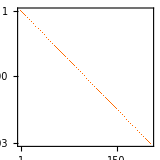
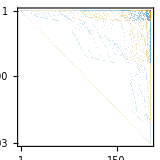
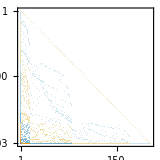
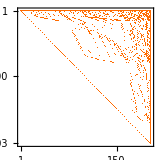
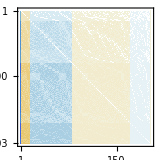
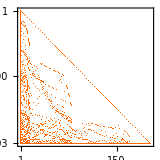
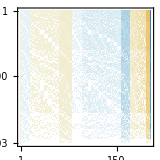
| C | E | G
C | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix6[base1,base2],ImageSize->160],{base1,allBases6},{base2,allBases6}],TableHeadings->{allBases6, allBases6},TableAlignments->{Center, Center}]
```

## Characterisc poly

```mathematica
Factor[CharacteristicPolynomial[ConversionMatrix6["E","G"],x]]
```

-(-1+x)^11 (1+x+x^2)^26 (1-6 x+4 x^2+31 x^3+12 x^4+31 x^5+4 x^6-6 x^7+x^8)^5 (1-x-x^2-7 x^3+23 x^4-22 x^5+23 x^6-7 x^7-x^8-x^9+x^10)^9 (1+23 x+286 x^2+2458 x^3+10538 x^4+19600 x^5+10538 x^6+2458 x^7+286 x^8+23 x^9+x^10)

```mathematica
Factor[CharacteristicPolynomial[ConversionMatrix["E","G"],x]]
```

(-1+x)^20 (1+x)^18 (1+x+x^2)^4 (1-3 x-28 x^2+62 x^3-28 x^4-3 x^5+x^6)

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=CharacteristicPolynomial[ConversionMatrix6[base1,base2],x]},
Factor[ch]
],{base1,base2}],{base1,allBases6}],{base2,allBases6}]],{base1,base2}]
```

-(-1+x)^203{C,C} | -(-1+x)^203{E,C} | -(-1+x)^203{G,C}
-(-1+x)^203{C,E} | -(-1+x)^203{E,E} | -(-1+x)^11 (1+x+x^2)^26 (1-6 x+4 x^2+31 x^3+12 x^4+31 x^5+4 x^6-6 x^7+x^8)^5 (1-x-x^2-7 x^3+23 x^4-22 x^5+23 x^6-7 x^7-x^8-x^9+x^10)^9 (1+23 x+286 x^2+2458 x^3+10538 x^4+19600 x^5+10538 x^6+2458 x^7+286 x^8+23 x^9+x^10){G,E}
-(-1+x)^203{C,G} | -(-1+x)^11 (1+x+x^2)^26 (1-6 x+4 x^2+31 x^3+12 x^4+31 x^5+4 x^6-6 x^7+x^8)^5 (1-x-x^2-7 x^3+23 x^4-22 x^5+23 x^6-7 x^7-x^8-x^9+x^10)^9 (1+23 x+286 x^2+2458 x^3+10538 x^4+19600 x^5+10538 x^6+2458 x^7+286 x^8+23 x^9+x^10){E,G} | -(-1+x)^203{G,G}

## Ranks d

```mathematica
Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[5]]}]]&]
```

{7174449,7174452,7174453,7174454,7174456,7174450,7174462,7174480,7174422,7174425,7174426,7174423,7174534,7174696,7175182,7173720,7173723,7173724,7173721,7173693,7173696,7173697,7173694,7176640,7181014,7194136,7233502,7115400,7115403,7115404,7115401,7115373,7115376,7115377,7115374,7114671,7114674,7114675,7114672,7114644,7114647,7114648,7114645,7351600,7705894,8768776,11957422}

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[5]]}]]&]}]]
```

16

```mathematica
CompleteGraph[2]//EdgeList
```

{1<->2}

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[2]]}]]&]}]]
```

202

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[3]]}]]&]}]]
```

171

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→202,3→171,4→81,5→16,6→1}

```mathematica
Table[203-k[[2]],{k,{2->202,3->171,4->81,5->16,6->1}}]
```

{1,32,122,187,202}

```mathematica
BellB[6]-BellB[1]
```

202

```mathematica
BellB[6]-10BellB[5]+35 BellB[4]-50BellB[3]+24BellB[2]
```

6

```mathematica
BellB[6]-3BellB[5]+2 BellB[4]
```

77

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Fold[And,Table[EdgeQ[allGraphs5[#,"graph"],e],{e,EdgeList[CompleteGraph[3]]}]]&]}]]
```

17

```mathematica
BellB[5]-3BellB[2]+BellB[1]
```

47

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

51

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],EdgeQ[allGraphs6[#,"graph"],1<->2]&]}]]
```

202

```mathematica
Select[Keys[allGraphs6],EdgeQ[allGraphs6[#,"graph"],1<->2]&]
```

{4782969,6377292,6908733,7085880,7144929,7164612,7171173,7173360,7174089,7174332,7174413,7174440,7174449,7174452,7174453,7174454,7174456,7174450,7174458,7174462,7174466,7174443,7174444,7174446,7174441,7174442,7174471,7174480,7174489,7174422,7174425,7174426,7174423,7174431,7174435,7174416,7174417,7174414,7174503,7174531,7174534,7174537,26451,13511622,13511623,13511620,13511628,13511632,13511613,13511614,13511611,13691034,13750840,13750843,13750846,13810649,13691037,13392000,13392009,13392012,13392013,13392016,13392010,13392003,13392004,13392006,13392001,13451808,13451817,13332204,13332207,13332208,13332209,13332205,13332198,13332199,13332196,13332197,14049864,14109672,14109673,14109674,14169481,14049865,14289097}
 |  |  |  |

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→151,3→77,4→26,5→6,6→1}

```mathematica
Table[Sum[BellB[6-k]StirlingS1[n,n-k],{k,0,n-1}],{n,6}]
```

{203,151,77,26,6,1}

```mathematica
TableForm[Table[BellB[n]//FactorInteger,{n,0,10}],TableDepth->2]
```

{1,1} |  |  | 
{1,1} |  |  | 
{2,1} |  |  | 
{5,1} |  |  | 
{3,1} | {5,1} |  | 
{2,2} | {13,1} |  | 
{7,1} | {29,1} |  | 
{877,1} |  |  | 
{2,2} | {3,2} | {5,1} | {23,1}
{3,1} | {7,1} | {19,1} | {53,1}
{5,2} | {4639,1} |  |

```mathematica
Table[
Table[
StirlingS1[n,n-k],{k,0,n}
],{n,1,15}
]//TableForm
```

1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -3 | 2 | 0 |  |  |  |  |  |  |  |  |  |  |  | 
1 | -6 | 11 | -6 | 0 |  |  |  |  |  |  |  |  |  |  | 
1 | -10 | 35 | -50 | 24 | 0 |  |  |  |  |  |  |  |  |  | 
1 | -15 | 85 | -225 | 274 | -120 | 0 |  |  |  |  |  |  |  |  | 
1 | -21 | 175 | -735 | 1624 | -1764 | 720 | 0 |  |  |  |  |  |  |  | 
1 | -28 | 322 | -1960 | 6769 | -13132 | 13068 | -5040 | 0 |  |  |  |  |  |  | 
1 | -36 | 546 | -4536 | 22449 | -67284 | 118124 | -109584 | 40320 | 0 |  |  |  |  |  | 
1 | -45 | 870 | -9450 | 63273 | -269325 | 723680 | -1172700 | 1026576 | -362880 | 0 |  |  |  |  | 
1 | -55 | 1320 | -18150 | 157773 | -902055 | 3416930 | -8409500 | 12753576 | -10628640 | 3628800 | 0 |  |  |  | 
1 | -66 | 1925 | -32670 | 357423 | -2637558 | 13339535 | -45995730 | 105258076 | -150917976 | 120543840 | -39916800 | 0 |  |  | 
1 | -78 | 2717 | -55770 | 749463 | -6926634 | 44990231 | -206070150 | 657206836 | -1414014888 | 1931559552 | -1486442880 | 479001600 | 0 |  | 
1 | -91 | 3731 | -91091 | 1474473 | -16669653 | 135036473 | -790943153 | 3336118786 | -9957703756 | 20313753096 | -26596717056 | 19802759040 | -6227020800 | 0 | 
1 | -105 | 5005 | -143325 | 2749747 | -37312275 | 368411615 | -2681453775 | 14409322928 | -56663366760 | 159721605680 | -310989260400 | 392156797824 | -283465647360 | 87178291200 | 0

```mathematica
TableForm[Table[
Table[Sum[BellB[max-k]StirlingS1[n,n-k],{k,0,n-1}],{n,max}],
{max,1,15}
]
]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
15 | 10 | 4 | 1 |  |  |  |  |  |  |  |  |  |  | 
52 | 37 | 17 | 5 | 1 |  |  |  |  |  |  |  |  |  | 
203 | 151 | 77 | 26 | 6 | 1 |  |  |  |  |  |  |  |  | 
877 | 674 | 372 | 141 | 37 | 7 | 1 |  |  |  |  |  |  |  | 
4140 | 3263 | 1915 | 799 | 235 | 50 | 8 | 1 |  |  |  |  |  |  | 
21147 | 17007 | 10481 | 4736 | 1540 | 365 | 65 | 9 | 1 |  |  |  |  |  | 
115975 | 94828 | 60814 | 29371 | 10427 | 2727 | 537 | 82 | 10 | 1 |  |  |  |  | 
678570 | 562595 | 372939 | 190497 | 73013 | 20878 | 4516 | 757 | 101 | 11 | 1 |  |  |  | 
4213597 | 3535027 | 2409837 | 1291020 | 529032 | 163967 | 38699 | 7087 | 1031 | 122 | 12 | 1 |  |  | 
27644437 | 23430840 | 16360786 | 9131275 | 3967195 | 1322035 | 338233 | 67340 | 10644 | 1365 | 145 | 13 | 1 |  | 
190899322 | 163254885 | 116393205 | 67310847 | 30785747 | 10949772 | 3017562 | 649931 | 111211 | 15415 | 1765 | 170 | 14 | 1 | 
1382958545 | 1192059223 | 865549453 | 516369838 | 247126450 | 93197715 | 27499083 | 6376149 | 1176701 | 175802 | 21652 | 2237 | 197 | 15 | 1

## Now for all graphs, not only with 6 vertices

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→202,3→171,4→81,5→16,6→1}

```mathematica
Table[203-k[[2]],{k,{2->202,3->171,4->81,5->16,6->1}}]
```

{1,32,122,187,202}

```mathematica
Total[Table[BaseCoeff6[k,"C"],{k,Keys[allGraphs6]}]]
```

{32768,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,17408,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,9280,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,5696,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,4968,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,3080,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1512,1082,1082,1082,1082,1082,1082,1082,1082,1082,1082,850,850,850,850,850,850,850,850,850,850,850,850,850,850,850,454,454,454,454,454,454,203}

```mathematica
Total[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]]
```

{32768,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,32,32,32,32,32,32,1}

```mathematica
FactorInteger[{32768,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,32,32,32,32,32,32,1}]//Sort//Tally
```

{{{{1,1}},1},{{{2,5}},6},{{{2,8}},15},{{{2,9}},25},{{{2,11}},60},{{{2,12}},35},{{{2,13}},45},{{{2,14}},15},{{{2,15}},1}}

```mathematica
Total[Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]
```

{1024,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,128,128,128,128,128,128,128,128,128,128,64,64,64,64,64,64,64,64,64,64,16,16,16,16,16,1}

```mathematica
Log[2,{32768,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,16384,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,8192,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,4096,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,2048,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,512,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,32,32,32,32,32,32,1}]//DeleteDuplicates
```

{15,14,13,12,11,9,8,5,0}